## Fourier series calculations and plot

```mathematica
2/l * Integrate[2 p/l (x-l/2)*Cos[n Pi x/l],{x,l/2,l},Assumptions->{l>0}]
```

(2 p (-2 Cos[(n π)/2]+2 Cos[n π]+n π Sin[n π]))/(n^2 π^2)

```mathematica
l=1;
p=1;
For[n=1,n≤20,n++,
a[n]=2/l * Integrate[2 p/l (x-l/2)*Cos[n Pi x/l],{x,l/2,l},Assumptions->{l>0}];
b[n]=2/l * Integrate[2 p/l (x-l/2)*Sin[n Pi x/l],{x,l/2,l},Assumptions->{l>0}];
];
```

```mathematica
a[0]=2/l * Integrate[2 p/l (x-l/2),{x,l/2,l},Assumptions->{l>0}];
```

```mathematica
f[x]=Sum[a[n]*Cos[n Pi x/l]+b[n]*Sin[n Pi x/l],{n,1,20}]+a[0]/2
```

1/4-(4 Cos[π x])/π^2+(2 Cos[2 π x])/π^2-(4 Cos[3 π x])/(9 π^2)-(4 Cos[5 π x])/(25 π^2)+(2 Cos[6 π x])/(9 π^2)-(4 Cos[7 π x])/(49 π^2)-(4 Cos[9 π x])/(81 π^2)+(2 Cos[10 π x])/(25 π^2)-(4 Cos[11 π x])/(121 π^2)-(4 Cos[13 π x])/(169 π^2)+(2 Cos[14 π x])/(49 π^2)-(4 Cos[15 π x])/(225 π^2)-(4 Cos[17 π x])/(289 π^2)+(2 Cos[18 π x])/(81 π^2)-(4 Cos[19 π x])/(361 π^2)+(2 (-2+π) Sin[π x])/π^2-Sin[2 π x]/π+(2 (2+3 π) Sin[3 π x])/(9 π^2)-Sin[4 π x]/(2 π)+(2 (-2+5 π) Sin[5 π x])/(25 π^2)-Sin[6 π x]/(3 π)+(2 (2+7 π) Sin[7 π x])/(49 π^2)-Sin[8 π x]/(4 π)+(2 (-2+9 π) Sin[9 π x])/(81 π^2)-Sin[10 π x]/(5 π)+(2 (2+11 π) Sin[11 π x])/(121 π^2)-Sin[12 π x]/(6 π)+(2 (-2+13 π) Sin[13 π x])/(169 π^2)-Sin[14 π x]/(7 π)+(2 (2+15 π) Sin[15 π x])/(225 π^2)-Sin[16 π x]/(8 π)+(2 (-2+17 π) Sin[17 π x])/(289 π^2)-Sin[18 π x]/(9 π)+(2 (2+19 π) Sin[19 π x])/(361 π^2)-Sin[20 π x]/(10 π)

```mathematica
F[x_]:=1/4-(4 Cos[π x])/π^2+(2 Cos[2 π x])/π^2-(4 Cos[3 π x])/(9 π^2)-(4 Cos[5 π x])/(25 π^2)+(2 Cos[6 π x])/(9 π^2)-(4 Cos[7 π x])/(49 π^2)-(4 Cos[9 π x])/(81 π^2)+(2 Cos[10 π x])/(25 π^2)-(4 Cos[11 π x])/(121 π^2)-(4 Cos[13 π x])/(169 π^2)+(2 Cos[14 π x])/(49 π^2)-(4 Cos[15 π x])/(225 π^2)-(4 Cos[17 π x])/(289 π^2)+(2 Cos[18 π x])/(81 π^2)-(4 Cos[19 π x])/(361 π^2)+(2 (-2+π) Sin[π x])/π^2-Sin[2 π x]/π+(2 (2+3 π) Sin[3 π x])/(9 π^2)-Sin[4 π x]/(2 π)+(2 (-2+5 π) Sin[5 π x])/(25 π^2)-Sin[6 π x]/(3 π)+(2 (2+7 π) Sin[7 π x])/(49 π^2)-Sin[8 π x]/(4 π)+(2 (-2+9 π) Sin[9 π x])/(81 π^2)-Sin[10 π x]/(5 π)+(2 (2+11 π) Sin[11 π x])/(121 π^2)-Sin[12 π x]/(6 π)+(2 (-2+13 π) Sin[13 π x])/(169 π^2)-Sin[14 π x]/(7 π)+(2 (2+15 π) Sin[15 π x])/(225 π^2)-Sin[16 π x]/(8 π)+(2 (-2+17 π) Sin[17 π x])/(289 π^2)-Sin[18 π x]/(9 π)+(2 (2+19 π) Sin[19 π x])/(361 π^2)-Sin[20 π x]/(10 π)
```

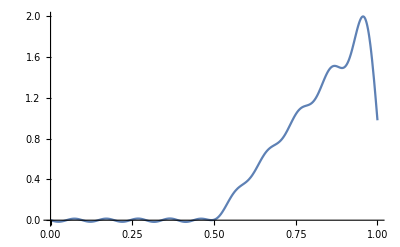

```mathematica
Plot[F[x],{x,0,1}]
```